# C. Sun Energy

```mathematica
(*Independent of θf, variable changed for Eγ*)
```

## Constants and Parameters (150MeV 0.5% bw)

```mathematica
(*Constants*)
re=2.8179403262*10^-15;
clight=299792458;
hbar=6.5821*10^-16; (*converted to eV, wavelength calc changed accordingly*)
me=0.511*10^6; (*mc^2 really*)
elecharge=1.60217662*10^-19;
```

```mathematica
(*Cases*)
CBETA150={Ee->150*10^6,Q->32*10^-12,Epulse->62*10^-6,λ->1064*10^-9,θcol->0.435*10^-3,ϕ->0,ϵnx->0.3*10^-6,βx->0.126976,σL->25*10^-6,ΔEe->5*10^-4,L->10};

CSUNBLACK={Ee->500*10^6,Q->130*10^-12,Epulse->3,λ->800*10^-9,θcol->(14/60)*10^-3,ϕ->0,ϵnx->0.489*10^-6,βx->0.01,σL->10*10^-6,ΔEe->2*10^-3,L->60};
CSUNRED={Ee->500*10^6,Q->130*10^-12,Epulse->3,λ->800*10^-9,θcol->(12/60)*10^-3,ϕ->0,ϵnx->0.489*10^-6,βx->0.01,σL->10*10^-6,ΔEe->2*10^-3,L->60};
CSUNBLUE={Ee->500*10^6,Q->130*10^-12,Epulse->3,λ->800*10^-9,θcol->(10/60)*10^-3,ϕ->0,ϵnx->0.489*10^-6,βx->0.01,σL->10*10^-6,ΔEe->2*10^-3,L->60};
CSUNPINK={Ee->500*10^6,Q->130*10^-12,Epulse->3,λ->800*10^-9,θcol->(8/60)*10^-3,ϕ->0,ϵnx->0.489*10^-6,βx->0.01,σL->10*10^-6,ΔEe->2*10^-3,L->60};
CSUNGREEN={Ee->500*10^6,Q->130*10^-12,Epulse->3,λ->800*10^-9,θcol->(4/60)*10^-3,ϕ->0,ϵnx->0.489*10^-6,βx->0.01,σL->10*10^-6,ΔEe->2*10^-3,L->60};
```

The cases shown are the CBETA ICS at 150MeV for the 0.5% bandwidth case and all the cases from Fig. 3 C. Sun et al PRSTAB 12, 062801 (2009). Emittance normalised, SI units used.

```mathematica
trialcase=CSUNGREEN;
```

## Observation Angle

```mathematica
θob[θx_,yc_,L_]:=Sqrt[θx^2+(yc/L)^2];
```

## SPE Intermediaries

```mathematica
(*Intermediary calculations for the scattered photon energy*)
γ[Ee_]:=Ee/me;
β[Ee_]:=Sqrt[1-1/γ[Ee]^2];
EL[λ_]:=(2*π*hbar*clight)/λ; (*in eV, using hbar*)
```

## Scattered Photon Energy Calc

```mathematica
Eγset[λ_,Ee_,ϕ_,θobs_]:=(EL[λ]*(1-β[Ee]*Cos[π-ϕ]))/(1-β[Ee]*Cos[θobs]+EL[λ]/Ee*(1-Cos[π-ϕ-θobs]));
```

```mathematica
Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase
```

401754.

```mathematica
Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase
```

5.51505×10^6

```mathematica
(*use 3 sigma of ΔEe to get 'head tail' as the compton edge is not sharp when you have an electron beam energy spread*)
```

## CSUN Preliminaries + Collimation

```mathematica
(*Preliminaries*)
Ne[Q_]:=Q/elecharge;
NL[Epulse_,λ_]:=Epulse/(EL[λ]*elecharge);
ϵx[Ee_,ϵnx_]:=ϵnx/γ[Ee];
k[λ_]:=EL[λ]/(hbar*clight);
zr[λ_,σL_]:=(π*σL^2)/λ;
σe[ΔEe_,Ee_]:=ΔEe*Ee; (*Conversion from relative*)
```

```mathematica
(*Collimation*)
R[L_,θcol_]:=L*θcol;
x0[L_,θcol_]:=R[L,θcol]; (*Condition for circular collimator*) 
y0[L_,θcol_]:=R[L,θcol];
```

## CSUN Intermediaries

```mathematica
a[λ_]:=EL[λ]/me;
γbar[λ_,Eγ_,θx_,yc_,L_]:=(2*Eγ*a[λ])/(4*EL[λ]-Eγ*θob[θx,yc,L]^2)*(1+Sqrt[1+(4*EL[λ]-Eγ*θob[θx,yc,L]^2)/(4*a[λ]^2*Eγ)]);
ξx[βx_,L_,λ_,Ee_,ϵnx_,σL_]:=1+(βx/L)^2+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
ζx[λ_,βx_,Ee_,ϵnx_,σL_]:=1+(2*k[λ]*βx*ϵx[Ee,ϵnx])/zr[λ,σL];
σθx[Ee_,ϵnx_,βx_,L_,λ_,σL_]:=Sqrt[(ϵx[Ee,ϵnx]*ξx[βx,L,λ,Ee,ϵnx,σL])/(βx*ζx[λ,βx,Ee,ϵnx,σL])];
σγ[ΔEe_,Ee_]:=σe[ΔEe,Ee]/me;
θxmax[λ_,Eγ_,yc_,L_]:=Sqrt[(4*EL[λ])/Eγ-(yc/L)^2];
```

## Prefactor

```mathematica
(*Prefactor*)
prefactor[L_,Q_,Epulse_,λ_,σL_,βx_,Ee_,ϵnx_,ΔEe_]:=(re^2*L^2*Ne[Q]*NL[Epulse,λ])/(2*π^2*hbar*clight*zr[λ,σL]*Sqrt[ζx[λ,βx,Ee,ϵnx,σL]]*σγ[ΔEe,Ee]*σθx[Ee,ϵnx,βx,L,λ,σL]);
prefactor[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe]/.trialcase
```

3.82321×10^14

## Separated Integral Terms

```mathematica
(*Separated Integral Terms, Each is calculated for the maximum scattered energy value, Plot of how each term looks 0 to θcol*)
```

```mathematica
(*Term 1*)
term1[λ_,Eγ_,θx_,yc_,L_]:=γbar[λ,Eγ,θx,yc,L]/(1+2*γbar[λ,Eγ,θx,yc,L]*a[λ]);
```

```mathematica
INTterm1[λ_,Eγ_,L_]:=NIntegrate[term1[λ,Eγ,θx,yc,L]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}];
```

```mathematica
Term1dat=Table[{Eγ,INTterm1[λ,Eγ,L]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,10}];
```

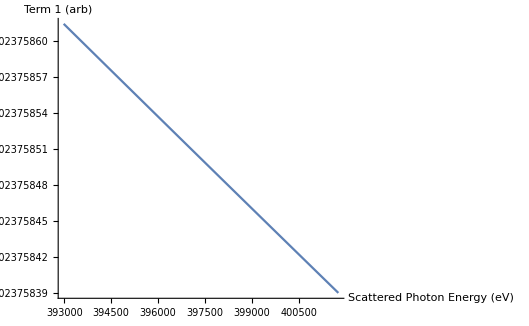

```mathematica
ListLinePlot[Term1dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 1 (arb)"}]
```

```mathematica
(*Term2*)
term2[λ_,Eγ_,θx_,yc_,L_]:=1/4*((4*γbar[λ,Eγ,θx,yc,L]^2*EL[λ])/(Eγ*(1+γbar[λ,Eγ,θx,yc,L]^2*θob[θx,yc,L]^2))+(Eγ*(1+γbar[λ,Eγ,θx,yc,L]^2*θob[θx,yc,L]^2))/(4*γbar[λ,Eγ,θx,yc,L]^2*EL[λ]));
```

```mathematica
INTterm2[λ_,Eγ_,L_]:=NIntegrate[term2[λ,Eγ,θx,yc,L]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}]
```

```mathematica
Term2dat=Table[{Eγ,INTterm2[λ,Eγ,L]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,10}];
```

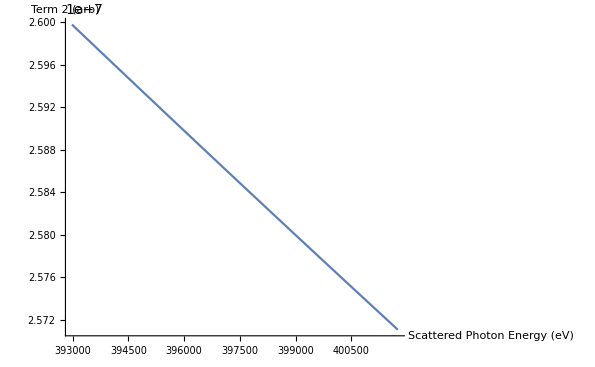

```mathematica
ListLinePlot[Term2dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 2 (arb)"}]
```

```mathematica
(*Term3*)
term3[θx_,xc_,L_,Ee_,ϵnx_,βx_,λ_,σL_,yc_,ΔEe_,Eγ_]:=Exp[(-(θx-xc/L)^2)/(2*σθx[Ee,ϵnx,βx,L,λ,σL]^2)-(γbar[λ,Eγ,θx,yc,L]-γ[Ee])^2/(2*σγ[ΔEe,Ee]^2)];
```

```mathematica
INTterm3[L_,Ee_,ϵnx_,βx_,λ_,σL_,ΔEe_,Eγ_]:=NIntegrate[term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}]
```

```mathematica
Term3dat=Table[{Eγ,INTterm3[L,Ee,ϵnx,βx,λ,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,100}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

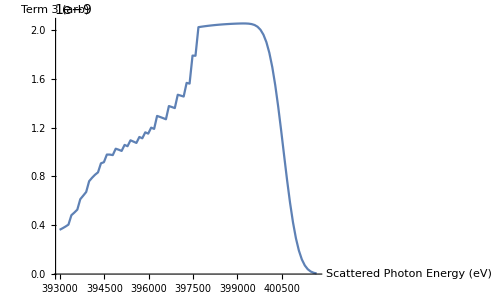

```mathematica
ListLinePlot[Term3dat,AxesLabel->{"Scattered Photon Energy (eV)","Term 3 (arb)"}]
```

## Integral Term

```mathematica
intterm[λ_,Ee_,θx_,yc_,L_,xc_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=term1[λ,Eγ,θx,yc,L]*term2[λ,Eγ,θx,yc,L]*term3[θx,xc,L,Ee,ϵnx,βx,λ,σL,yc,ΔEe,Eγ];
```

```mathematica
INTterm[λ_,Ee_,L_,ϵnx_,βx_,σL_,ΔEe_,Eγ_]:=NIntegrate[intterm[λ,Ee,θx,yc,L,xc,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase,{yc,-y0[L,θcol]/.trialcase,y0[L,θcol]/.trialcase},{xc,-x0[L,θcol]/.trialcase,x0[L,θcol]/.trialcase},{θx,-θxmax[λ,Eγ,yc,L]/.trialcase,θxmax[λ,Eγ,yc,L]/.trialcase}];
```

```mathematica
Intdat=Table[{Eγ,INTterm[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,100}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

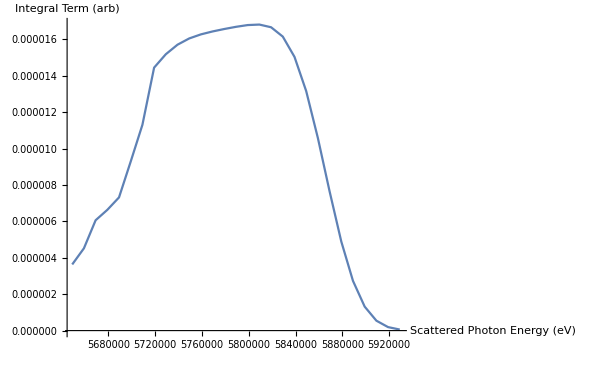

```mathematica
ListLinePlot[Intdat,AxesLabel->{"Scattered Photon Energy (eV)","Integral Term (arb)"}]
```

## C. Sun Calculation

```mathematica
(*Full Calc + Evaluation*)
dNγdEγ[L_,Q_,Epulse_,λ_,σL_,βx_,Ee_,ϵnx_,ΔEe_,Eγ_]:=prefactor[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe]*INTterm[λ,Ee,L,ϵnx,βx,σL,ΔEe,Eγ];
```

```mathematica
SpecDen=Table[{Eγ*10^-6,dNγdEγ[L,Q,Epulse,λ,σL,βx,Ee,ϵnx,ΔEe,Eγ]/.trialcase},{Eγ,Eγset[λ,Ee*(1-3*ΔEe),ϕ,θcol]/.trialcase,Eγset[λ,Ee*(1+3*ΔEe),ϕ,0]/.trialcase,10000}];
```

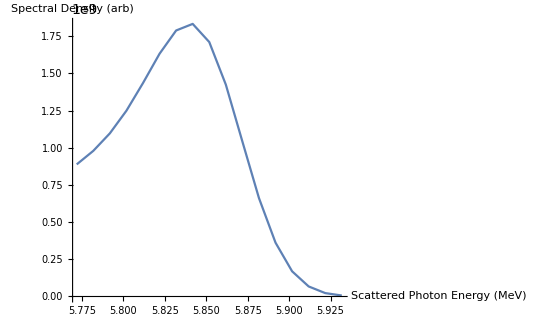

```mathematica
ListLinePlot[SpecDen,AxesLabel->{"Scattered Photon Energy (MeV)","Spectral Density (arb)"}]
```

## α Collimation Parameter

```mathematica
α[Ee_,θcol_,ΔEe_]:=(γ[Ee]^2*θcol^2)/(2*Sqrt[2*Log[2]]*2*ΔEe);
```

```mathematica
α[Ee,θcol,ΔEe]/.trialcase
```

6.92407

## Saving Spectrum

```mathematica
SetDirectory["C:/Users/user/Documents/Wolfram Mathematica/Spectrum_Data"];
SpecDen>>"CSUN_GREEN.txt";
```

## Plotting Cases from File

```mathematica
(*Importing*)
CBETA150=<<"CBETA150.txt";

CSUNBLACK=<<"CSUN_BLACK.txt";
CSUNRED=<<"CSUN_RED.txt";
CSUNBLUE=<<"CSUN_BLUE.txt";
CSUNPINK=<<"CSUN_PINK.txt";
CSUNGREEN=<<"CSUN_GREEN.txt";
```

```mathematica
(*Plotting*)
```

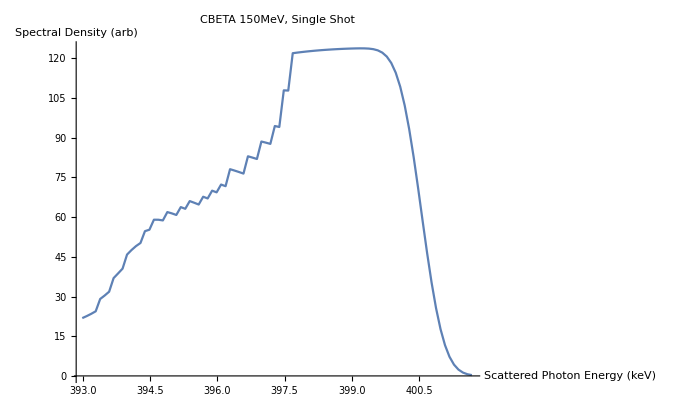

```mathematica
ListLinePlot[CBETA150,AxesLabel->{"Scattered Photon Energy (keV)","Spectral Density (arb)"},PlotLabel->"CBETA 150MeV, Single Shot" ]
```

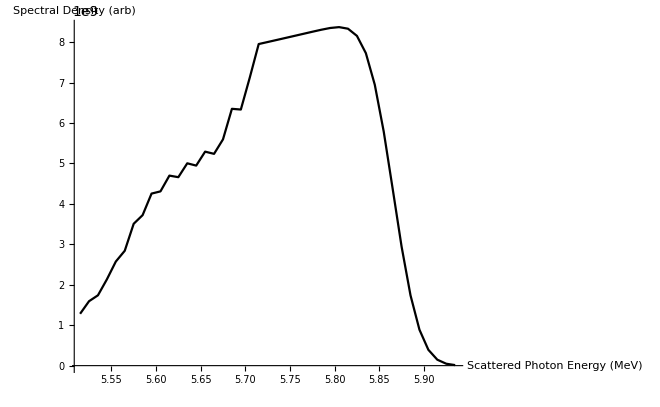

```mathematica
ListLinePlot[CSUNBLACK,AxesLabel->{"Scattered Photon Energy (MeV)","Spectral Density (arb)"},PlotStyle->Black]
```

```mathematica
ListLinePlot[{CSUNBLACK,CSUNRED,CSUNBLUE,CSUNPINK,CSUNGREEN},AxesLabel->{"Scattered Photon Energy (MeV)","Spectral Density (arb)"},PlotStyle->{Black,Red,Blue,Pink,Green},PlotLabel->"C. Sun Fig. 3" ]
```

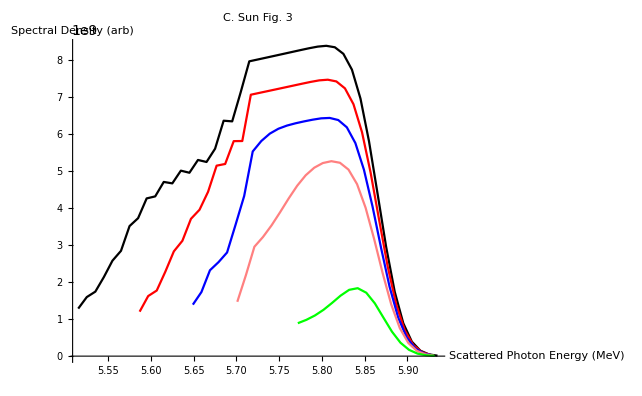
```mathematica
-Graphics--Graphics-
```

Runs so much faster. Graphs show weird numerical behaviour at increasing collimation angle, still seeing oscillatory integral error. Head of spectrum not knife-edge ‘Compton Edge’ because of energy spread. Intensity variation not understood yet (Q, Epulse, β* ,σL  all unknown and guessed at using assumption of a linac (based on low emittance) and high powered laser system. This potentially could be because each case is optimised for a fixed bandwidth (like on my tuning curves F-BW is independent of beam energy for correct β*-θcol) and therefore intensity is constant?